```mathematica
coordinatesPath = "/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/WolframVisualization/coordinates.txt";
firstMethodPath = "/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/WolframVisualization/Convex Hull Points (Method I).txt";
secondMethodPath = "/Users/arsenytokarev/Desktop/ConvexHull_BMSTU/WolframVisualization/Convex Hull Points (Method II).txt";

numberOfPoints = ToExpression[
Import[coordinatesPath, {"Lines", 1} ]
];
```

```mathematica
points = {};
For[i = 2, i < numberOfPoints* 2 + 2, i+= 2, 
AppendTo[points,Point[ToExpression[
Take[
Import[coordinatesPath,"Words"],{i, i+1}]
]
]
]
]
```

```mathematica
numberOfConvexHullPoints = ToExpression[Import[firstMethodPath, {"Lines", 1}]];
convexHullPoints = {};
For[i = 2, i < numberOfConvexHullPoints * 2 + 2, i+= 2, AppendTo[convexHullPoints,ToExpression[Take[Import[firstMethodPath, "Words"],{i, i+1}]]]
]
AppendTo[convexHullPoints, Part[convexHullPoints, 1]]
```

{{9825.5,7533.56},{9346.93,-5194.16},{726.859,-8847.07},{-2189.59,-6788.65},{-8976.56,-605.643},{-7011.91,7621.98},{6867.73,9304.36},{9825.5,7533.56}}

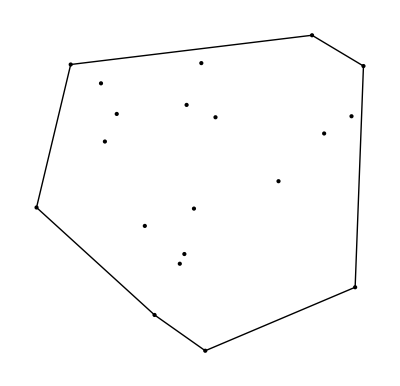

```mathematica
Graphics[{points,Line[convexHullPoints]}]
```